```mathematica
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];
Needs["FunctionApproximations`"];
```

```mathematica
ExtData=Import["/home/tom/Documents/škola/bakalářka/model_S.dat","Data"];
```

```mathematica
TempExt=Interpolation[Reap[For[i=1,i≤Length[ExtData],i++,
Sow[
{ExtData[[i]][[1]],ExtData[[i]][[2]]}]
]][[2]][[1]],InterpolationOrder->1];
pExt=Interpolation[Reap[For[i=1,i≤Length[ExtData],i++,
Sow[
{ExtData[[i]][[1]],ExtData[[i]][[3]]}]
]][[2]][[1]],InterpolationOrder->1];
ρExt=Interpolation[Reap[For[i=1,i≤Length[ExtData],i++,
Sow[
{6.959894528 10^8-ExtData[[i]][[1]],ExtData[[i]][[4]]}]
]][[2]][[1]],InterpolationOrder->1];
Clear[g];
gz0=NIntegrate[G 4π ρExt[r] r^2,{r,0,6.959894528 10^8-z0}]/((6.959894528 10^8-z0)^2);
g[z_]:=gz0+NIntegrate[G 4π ρExt[r] r^2,{r,6.959894528 10^8-z0,6.959894528 10^8-z}]/((6.959894528 10^8-z)^2) (*tohle je hodne prasacky a je potreba doladit*)
gTab=Table[{z,g[z]},{z,0,z0,1000000}];
Clear[g];
g=Interpolation[gTab,InterpolationOrder->1];
```

{{0,283.737},{1000000,283.737},{2000000,283.737},{3000000,283.737},{4000000,283.737},{5000000,283.737},{6000000,283.737},{7000000,283.737},{8000000,283.736},{9000000,283.736},{10000000,283.735},{11000000,283.735},{12000000,283.734}}

```mathematica
NIntegrate[G 4π ρExt[r] r^2,{r,6.959894528 10^8-10^6,6.959894528 10^8-0}]
```

3.5838×10^11

```mathematica
σ=5.670373 10^-8;
k=1.3806488 10^-23;
G=6.67384 10^-11;
a=0.125;
b=0.5;
f=1.5;
α=0.2;
R=8.3144621;
χ=2.18 10^-18;
μ0=(0.6 1+0.4 4);
μ=μ0 ;
Φ=10^29;
Δt=60 30;
vodik = 0.6;
```

```mathematica
ρ=ρExt;
Temp=TempExt;
x[x_]:=0.5
B0=10.;
z0=12 10^6;
κ=10^-4;
```

```mathematica
p=NDSolve[{P'[z]==(10^-3 μ/(μ+x[z]) P[z])/(R Temp[z])g[z],P[z0 ]==pExt[z0]-B0^2/(8π)},P,{z,0,z0},Method->{"StiffnessSwitching","NonstiffTest"->False}][[1]][[1]][[2]];
Δp[z_]:=pExt[z]-p[z]
y=NDSolve[{Φ/(2π)sqrtB[z]sqrtB''[z]==sqrtB[z]^4-8π Δp[z],sqrtB[z0]==√B0,sqrtB'[z0]==0},sqrtB,{z,0,z0},Method->{"StiffnessSwitching","NonstiffTest"->False}][[1]][[1]][[2]];
Clear[TempNew]
TempNew[z_]:=Temp[z]-1/(cp[z]ρ[z])(Frad'[z]+Fconv'[z]) Δt
TempNew=Temp;
```

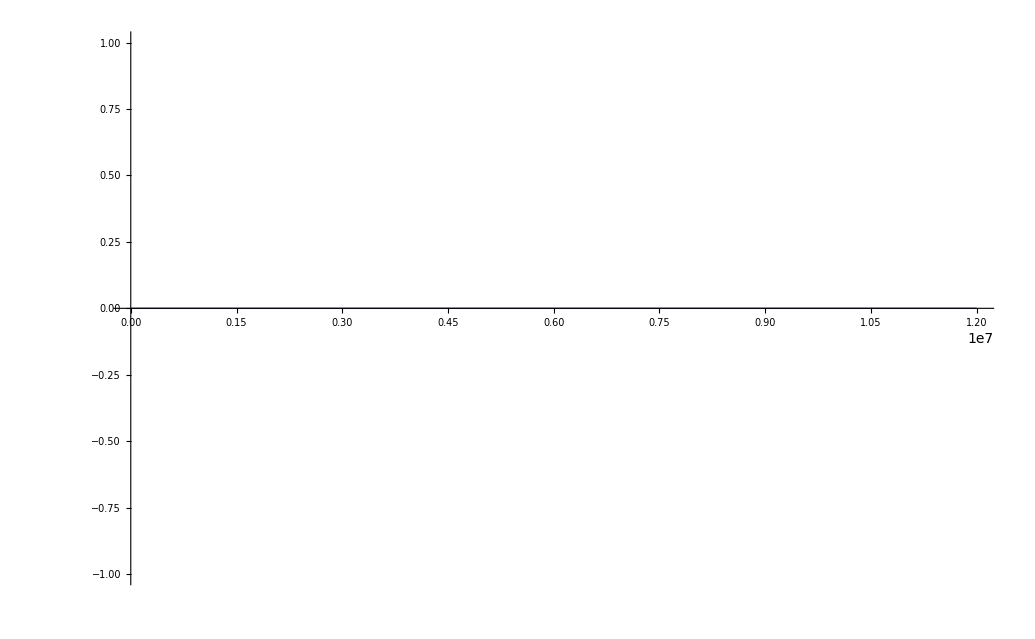

```mathematica
Plot[{Temp[z]-TempExt[z]},{z,0,z0},PlotRange->All]
```

```mathematica
(*H[z_]:=(1/p[z] p'[z])^-1*)
H[z_]:=(R Temp[z])/(μ g[z])
x[z_]:=Exp[5/2 Log[Temp[z],10]-(13.53 5040)/Temp[z]-0.48-Log[vodik,10]-Log[p[z],10]-Log[μ0,10]]/(1+Exp[5/2 Log[Temp[z],10]-(13.53 5040)/Temp[z]-0.48-Log[vodik,10]-Log[p[z],10]-Log[μ0,10]])(*ionization degree*)
(*μ[z_]:=μ0/(1+x[z])*)
cp[z_]:=R/μ(5/2+1/2 x[z](1-x[z])(5/2+χ/(k Temp[z]))^2) (*tyto tri rovnice jsou z Deinzer 1965*)
logGrad[z_]:=p[z]/Temp[z] Temp'[z]/p'[z]
adGrad[z_]:=(2+x[z](1-x[z])(5/2+χ/(k Temp[z])))/(5+x[z](1-x[z])(5/2+χ/(k Temp[z]))^2)
u[z_]:=1/(f √a)(α^-2 12σ Temp[z]^3)/(cp[z] ρ[z] κ H[z]^2)√(H[z]/g[z])
radEx[z_]:=adGrad[z]-2 u[z]^2+2u[z] √(logGrad[z]-adGrad[z]+u[z]^2)
Frad[z_]:=(16 σ Temp[z]^3)/(3κ ρ[z])Temp'[z]
Fconv[z_]:=-b √a √(R/μ)√α ρ[z] cp[z] Temp[z]^(3/2)(logGrad[z]-radEx[z])^(3/2)
```